```mathematica
Needs@"CellsToTeX`"
f[x,y] = x^2 y^2 (x+y)^2 - 4 *x* (y+x)^2 - 4*x^4 * y^4 - 27 * x^4 k^2 + 18* x^3 y^2 (x+y)
```

-27 k^2 x^4-4 x^4 y^4+18 x^3 y^2 (x+y)-4 x (x+y)^2+x^2 y^2 (x+y)^2

```mathematica
-27 k^2 x^4-4 x^4 y^4+18 x^3 y^2 (x+y)-4 x (x+y)^2+x^2 y^2 (x+y)^2
g[r,k] = Discriminant[(-r/k x^3+r x^2-x(1+r/k)+r),x]
```

-27 k^2 x^4-4 x^4 y^4+18 x^3 y^2 (x+y)-4 x (x+y)^2+x^2 y^2 (x+y)^2

(-4 k^3 r-12 k^2 r^2+k^4 r^2-12 k r^3+20 k^3 r^3-4 r^4-8 k^2 r^4-4 k^4 r^4)/k^4

```mathematica
(-4 k^3 r-12 k^2 r^2+k^4 r^2-12 k r^3+20 k^3 r^3-4 r^4-8 k^2 r^4-4 k^4 r^4)/k^4
Plot3D[g[r,k],{r,-5,5},{k,-5,5}]
```

(-4 k^3 r-12 k^2 r^2+k^4 r^2-12 k r^3+20 k^3 r^3-4 r^4-8 k^2 r^4-4 k^4 r^4)/k^4

-Graphics3D-

```mathematica
Rasterize[%31,"Image"]
```

```mathematica
Show[%31,AxesStyle->Black]
```

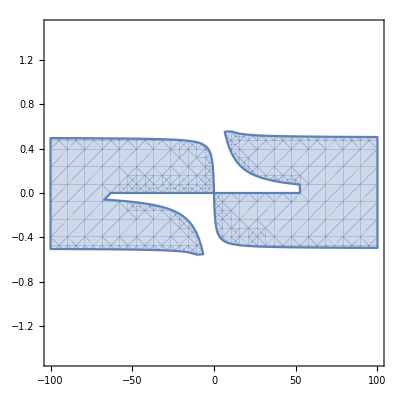

```mathematica
RegionPlot[k^2 r (12 k r^2+4 r^3+k^3 (4-20 r^2)+4 k^2 r (3+2 r^2)+k^4 r (-1+4 r^2))<0,{k,-100,100},{r,-1.5,1.5}]
```

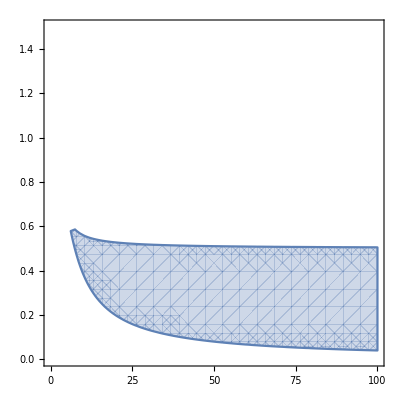

```mathematica
RegionPlot[k^2 r (12 k r^2+4 r^3+k^3 (4-20 r^2)+4 k^2 r (3+2 r^2)+k^4 r (-1+4 r^2))<0,{k,0,100},{r,0,1.5}]
```

```mathematica
"/home/mitchell/Documents/masters/statmech/fourth/discriminant.svg"
Export["/home/mitchell/Documents/masters/statmech/fourth/discriminant.jpg",%31,"JPG"]
```

```mathematica
g1[r,k] = Discriminant[(-r/k) x^3+r x^2-x (1+r/k)+r,x] u<0
```

```mathematica
Reduce[k^2 r (12 k r^2+4 r^3+k^3 (4-20 r^2)+4 k^2 r (3+2 r^2)+k^4 r (-1+4 r^2)) u>0,{k,r,u}]
```